```mathematica
(* resting potential is set to zero *)
```

```mathematica
(* Case of current input *)
```

```mathematica
cap=1;
Vna=115;
Vk=-12;
Vl=10.6;
Gna=120;
Gk=36;
Gl=0.3;

sde=0.5;
sre=3;
sdi=0.5;
sri=7;
Vge=65;
Vgi=-15;
fe=0.04;
fi=0.04;
see=0.05;

fan[v_]:=(0.1-0.01 v)/(Exp[1-0.1 v]-1)
fam[v_]:=(2.5-0.1 v)/(Exp[2.5-0.1 v]-1)
fah[v_]:=0.07 Exp[-v/20]
fbn[v_]:=0.125 Exp[-v/80]
fbm[v_]:=4 Exp[-v/18]
fbh[v_]:=1/(Exp[3-0.1 v]+1)
```

```mathematica
Clear[T,I1ext,SimuHHcurrent]
SimuHHcurrent[innerI1ext_,innerT_]:=
Module[{I1ext=innerI1ext,T=innerT},
ns=NDSolve[{
cap*V1'[t]==-(V1[t]-Vna) Gna h1[t] m1[t]^3-(V1[t]-Vk) Gk n1[t]^4-(V1[t]-Vl) Gl+I1ext[t],
m1'[t]==(1-m1[t]) fam[V1[t]]-m1[t] fbm[V1[t]],
h1'[t]==(1-h1[t]) fah[V1[t]]-h1[t] fbh[V1[t]],
n1'[t]==(1-n1[t]) fan[V1[t]]-n1[t] fbn[V1[t]],
V1[0]==0,
m1[0]==0.05293248525724958,
h1[0]==0.5961207535084603,
n1[0]==0.3176769140606974
},{V1,m1,h1,n1},{t,0,T}];
ns[[1]]
]
```

```mathematica
(* Case of poisson input, N=1 *)
```

```mathematica
Clear[simuHHpoisson1]
simuHHpoisson1[tbinp0_,T00_]:=
Module[{tbinp=tbinp0,T0=T00,Tnow,paraminit,flistV1,i,T,ns},
Tnow=0;
flistV1={};
paraminit={v1->0,ionm1->0.05293248525724958,ionh1->0.5961207535084603,ionn1->0.3176769140606974,gE1->0,hE1->0,gI1->0,hI1->0};
For[i=0,i≤Length[tbinp],i++,
T=If[i==0,
tbinp[[1]][[2]],
If[i==Length[tbinp],
T0-tbinp[[i]][[2]],tbinp[[i+1]][[2]]-tbinp[[i]][[2]]
]
];
ns=NDSolve[{
cap*V1'[t]==-(V1[t]-Vna) Gna h1[t] m1[t]^3-(V1[t]-Vk) Gk n1[t]^4-(V1[t]-Vl) Gl-(V1[t]-Vge) G1e[t]-(V1[t]-Vgi) G1i[t],
m1'[t]==(1-m1[t]) fam[V1[t]]-m1[t] fbm[V1[t]],
h1'[t]==(1-h1[t]) fah[V1[t]]-h1[t] fbh[V1[t]],
n1'[t]==(1-n1[t]) fan[V1[t]]-n1[t] fbn[V1[t]],
G1e'[t]==-G1e[t]/sde+H1e[t],
H1e'[t]==-H1e[t]/sre,
G1i'[t]==-G1i[t]/sdi+H1i[t],
H1i'[t]==-H1i[t]/sri,
V1[Tnow]==v1/.paraminit,
m1[Tnow]==ionm1/.paraminit,
h1[Tnow]==ionh1/.paraminit,
n1[Tnow]==ionn1/.paraminit,
G1e[Tnow]==gE1/.paraminit,
H1e[Tnow]==hE1/.paraminit,
G1i[Tnow]==gI1/.paraminit,
H1i[Tnow]==hI1/.paraminit
},{V1,m1,h1,n1,G1e,H1e,G1i,H1i},
{t,Tnow,Tnow+T}
];
paraminit={v1->V1[t],ionm1->m1[t],ionh1->h1[t],ionn1->n1[t],gE1->G1e[t],hE1->H1e[t]+fe,gI1->G1i[t],hI1->H1i[t]+fi*0}/.t->Tnow+T/.ns[[1]];
AppendTo[flistV1,{V1[t]/.ns[[1]],Tnow<t≤Tnow+T}];
Tnow+=T;
];
(* faster than directly return Piecewise[flistV1] *)
{V1->(tt↦(Piecewise[flistV1]/.{t->tt}))}
]
```

```mathematica
(* Case of poisson input, N=2 *)
```

```mathematica
Clear[simuHHpoisson2]
simuHHpoisson2[tbinp0_,T00_]:=
Module[{tbinp=tbinp0,T0=T00,Tnow,paraminit,flistV1,flistV2,i,T,ns},
Tnow=0;
flistV1={};
flistV2={};
paraminit={
v1->0,ionm1->0.05293248525724958,ionh1->0.5961207535084603,ionn1->0.3176769140606974,gE1->0,hE1->0,gI1->0,hI1->0,v2->0,ionm2->0.05293248525724958,ionh2->0.5961207535084603,ionn2->0.3176769140606974,gE2->0,hE2->0,gI2->0,hI2->0};
For[i=0,i≤Length[tbinp],i++,
T=If[i==0,
tbinp[[1]][[2]],
If[i==Length[tbinp],
T0-tbinp[[i]][[2]],tbinp[[i+1]][[2]]-tbinp[[i]][[2]]
]
];
ns=NDSolve[{
cap*V1'[t]==-(V1[t]-Vna) Gna h1[t] m1[t]^3-(V1[t]-Vk) Gk n1[t]^4-(V1[t]-Vl) Gl-(V1[t]-Vge) G1e[t]-(V1[t]-Vgi) G1i[t],
m1'[t]==(1-m1[t]) fam[V1[t]]-m1[t] fbm[V1[t]],
h1'[t]==(1-h1[t]) fah[V1[t]]-h1[t] fbh[V1[t]],
n1'[t]==(1-n1[t]) fan[V1[t]]-n1[t] fbn[V1[t]],
G1e'[t]==-G1e[t]/sde+H1e[t],
H1e'[t]==-H1e[t]/sre,
G1i'[t]==-G1i[t]/sdi+H1i[t],
H1i'[t]==-H1i[t]/sri,
V1[Tnow]==v1/.paraminit,
m1[Tnow]==ionm1/.paraminit,
h1[Tnow]==ionh1/.paraminit,
n1[Tnow]==ionn1/.paraminit,
G1e[Tnow]==gE1/.paraminit,
H1e[Tnow]==hE1/.paraminit,
G1i[Tnow]==gI1/.paraminit,
H1i[Tnow]==hI1/.paraminit,cap*V2'[t]==-(V2[t]-Vna) Gna h2[t] m2[t]^3-(V2[t]-Vk) Gk n2[t]^4-(V2[t]-Vl) Gl-(V2[t]-Vge) G2e[t]-(V2[t]-Vgi) G2i[t],
m2'[t]==(1-m2[t]) fam[V2[t]]-m2[t] fbm[V2[t]],
h2'[t]==(1-h2[t]) fah[V2[t]]-h2[t] fbh[V2[t]],
n2'[t]==(1-n2[t]) fan[V2[t]]-n2[t] fbn[V2[t]],
G2e'[t]==-G2e[t]/sde+H2e[t],
H2e'[t]==-H2e[t]/sre+see*1/(1+Exp[-(V1[t]-85)/2]),
G2i'[t]==-G2i[t]/sdi+H2i[t],
H2i'[t]==-H2i[t]/sri,
V2[Tnow]==v2/.paraminit,
m2[Tnow]==ionm2/.paraminit,
h2[Tnow]==ionh2/.paraminit,
n2[Tnow]==ionn2/.paraminit,
G2e[Tnow]==gE2/.paraminit,
H2e[Tnow]==hE2/.paraminit,
G2i[Tnow]==gI2/.paraminit,
H2i[Tnow]==hI2/.paraminit
},{V1,m1,h1,n1,G1e,H1e,G1i,H1i,V2,m2,h2,n2,G2e,H2e,G2i,H2i},
{t,Tnow,Tnow+T}
];
paraminit={v1->V1[t],ionm1->m1[t],ionh1->h1[t],ionn1->n1[t],gE1->G1e[t],hE1->H1e[t]+Boole[If[i<Length[tbinp],tbinp[[i+1]][[1]]==0,False]]*fe,gI1->G1i[t],hI1->H1i[t]+fi*0,v2->V2[t],ionm2->m2[t],ionh2->h2[t],ionn2->n2[t],gE2->G2e[t],hE2->H2e[t]+Boole[If[i<Length[tbinp],tbinp[[i+1]][[1]]==1,False]]*fe,gI2->G2i[t],hI2->H2i[t]+fi*0
}/.t->Tnow+T/.ns[[1]];
If[i==0,
AppendTo[flistV1,{V1[t]/.ns[[1]],Tnow≤t≤Tnow+T}];
AppendTo[flistV2,{V2[t]/.ns[[1]],Tnow≤t≤Tnow+T}];
,
AppendTo[flistV1,{V1[t]/.ns[[1]],Tnow<t≤Tnow+T}];
AppendTo[flistV2,{V2[t]/.ns[[1]],Tnow<t≤Tnow+T}];
];
Tnow+=T;
];
{V1->(tt↦(Piecewise[flistV1]/.{t->tt})),V2->(tt↦(Piecewise[flistV2]/.{t->tt}))}
]
```

```mathematica
(* Cases *)
stv=0.5;
simudt=2^-9;
pathtest="testdata/";
```

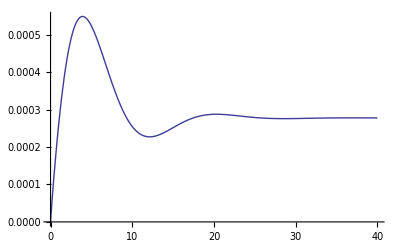

```mathematica
(* ic_case=0 *)

I1ext2[t_]:=2.3*HeavisideTheta[t-0.1];
I1ext1[t_]:=13.279*HeavisidePi[2 (t-0.8)];
I1ext0[t_]:=0;
T0=40;
sl0=SimuHHcurrent[I1ext0,T0];
tb=Table[Evaluate[V1[stv (j-2*simudt)]/.sl0],{j,1,80}];
Export[NotebookDirectory[]<>pathtest<>"tb0.txt",tb];
Plot[Evaluate[V1[t]/.sl0],{t,0,T0},PlotRange->All]
```

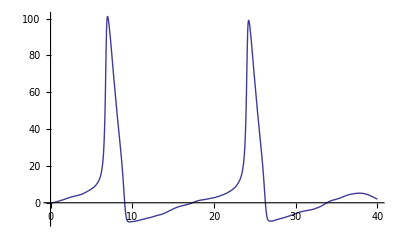

```mathematica
(* ic_case=1 *)

tbinp=Import[NotebookDirectory[]<>pathtest<>"spe1.txt","Table"];
T0=40;
see=0.05;
fe=0.04;
sl1=simuHHpoisson1[tbinp,T0];
tb=Table[Evaluate[V1[stv (j-2*simudt)]/.sl1],{j,1,80}];
Export[NotebookDirectory[]<>pathtest<>"tb1.txt",tb];
Plot[Evaluate[V1[x]/.sl1],{x,0,T0},PlotRange->All]
```

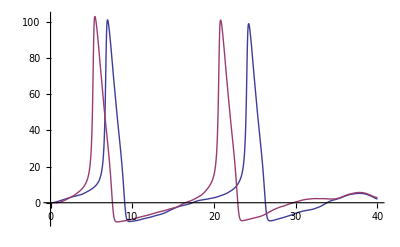

```mathematica
(* ic_case=2 *)

tbinp=Import[NotebookDirectory[]<>pathtest<>"spe2.txt","Table"];
T0=40;
see=0.05;
fe=0.04;
sl2=simuHHpoisson2[tbinp,T0];
tb=Table[Evaluate[{V1[t]/.sl2,V2[t]/.sl2}/.t->stv (j-2*simudt)],{j,1,80}];
Export[NotebookDirectory[]<>pathtest<>"tb2.txt",tb,"Table"];
Plot[Evaluate[{V1[t]/.sl2,V2[t]/.sl2}],{t,0,T0},PlotRange->All]
```

```mathematica
(* Synaptic responds test *)
```

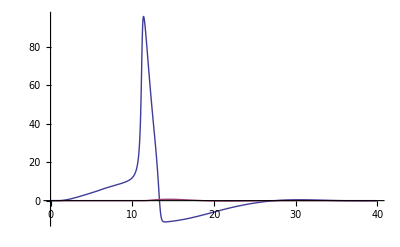

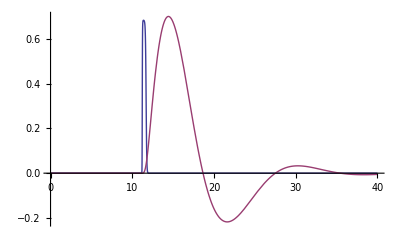

{0.699154,{t→14.4253}}

```mathematica
see=0.05;
fe=0.04;
Vl=10.6;
Vl=10.59892097;
gV[V_]:=(13.7 see)/(1+Exp[-(V-85)/2])
(*tbinp=Import[NotebookDirectory[]<>"spe2.txt","Table"];
T0=40;
tbinp=Delete[tbinp,Position[tbinp[[;;,1]],1]];*)
tbinp=Table[{0,1.06*j},{j,5}];
sl2=simuHHpoisson2[tbinp,T0];
Plot[Evaluate[{V1[t]/.sl2,V2[t]/.sl2}],{t,0,T0},PlotRange->All]
Plot[Evaluate[{gV[V1[t]]/.sl2,V2[t]/.sl2}],{t,0,T0},PlotRange->All]
FindMaximum[{Evaluate[V2[t]/.sl2],0<t<T0},{t,15}]
```

```mathematica
(* Poisson Input responds test *)
```

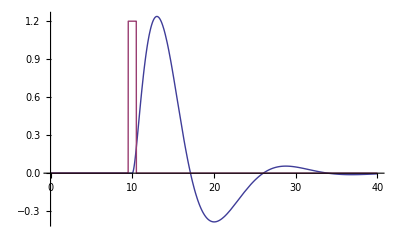

{1.23741,{t→13.0128}}

```mathematica
tbinp={{0,10}};
T0=40;
fe=0.04;
sl=simuHHpoisson1[tbinp,T0];
Plot[Evaluate[{V1[x]/.sl,30 fe UnitBox[x-tbinp[[1]][[2]]]}],{x,0,T0},PlotRange->All]
FindMaximum[{Evaluate[V1[t]/.sl],0<t<T0},{t,15}]
```